```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,-1.39432×10^8},{60,-1.45455×10^8},{70,-1.48283×10^8},{80,-1.49758×10^8},{90,-1.49727×10^8},{100,-1.50042×10^8},{110,-1.49077×10^8},{120,-1.47932×10^8},{130,-1.43733×10^8},{140,-1.42519×10^8},{150,-1.41307×10^8},{160,-1.40747×10^8},{170,-1.39526×10^8},{180,-1.3817×10^8},{190,-1.36338×10^8},{200,-1.3587×10^8},{210,-1.37256×10^8},{220,-1.33779×10^8},{230,-1.3583×10^8},{240,-1.34709×10^8},{250,-1.3381×10^8},{260,-1.32756×10^8},{270,-1.34535×10^8},{280,-1.33711×10^8},{290,-1.32924×10^8},{300,-1.32162×10^8},{310,-1.33066×10^8},{320,-1.20257×10^8},{330,-1.19632×10^8},{340,-1.18858×10^8},{350,-1.14196×10^8},{360,-1.15446×10^8},{370,-1.02561×10^8},{380,-1.01421×10^8},{390,-9.76942×10^7},{400,-9.73045×10^7},{410,-9.9434×10^7},{420,-9.90039×10^7},{430,-1.00641×10^8},{440,-9.05428×10^7},{450,-9.00695×10^7},{460,-8.97717×10^7},{470,-8.93236×10^7},{480,-8.90461×10^7},{490,-9.14045×10^7},{500,-9.05516×10^7},{510,-9.02928×10^7},{520,-8.83019×10^7},{530,-8.80539×10^7},{540,-8.78128×10^7},{550,-7.93655×10^7},{560,-7.91712×10^7},{570,-7.89827×10^7},{580,-7.87242×10^7},{590,-7.8627×10^7},{600,-7.90522×10^7},{610,-7.88851×10^7},{620,-7.74022×10^7},{630,-7.72506×10^7},{640,-7.72271×10^7},{650,-7.70824×10^7},{660,-7.87912×10^7},{670,-7.7367×10^7},{680,-7.44704×10^7},{690,-7.43411×10^7},{700,-7.42142×10^7},{710,-7.41699×10^7},{720,-7.40463×10^7},{730,-7.39255×10^7},{740,-7.37977×10^7},{750,-6.53701×10^7},{760,-6.52773×10^7},{770,-6.46996×10^7},{780,-6.51849×10^7},{790,-6.50976×10^7},{800,-6.50124×10^7},{810,-6.56751×10^7},{820,-6.55825×10^7},{830,-6.54957×10^7},{840,-6.54072×10^7},{850,-6.53444×10^7},{860,-6.52786×10^7},{870,-6.51937×10^7},{880,-6.51104×10^7},{890,-6.49979×10^7},{900,-6.49177×10^7},{910,-6.4838×10^7},{920,-6.4759×10^7},{930,-6.46803×10^7},{940,-6.4602×10^7},{950,-6.4524×10^7},{960,-6.44461×10^7},{970,-6.43683×10^7},{980,-6.42905×10^7},{990,-6.24314×10^7},{1000,-6.23554×10^7},{1010,-6.22791×10^7},{1020,-6.38734×10^7},{1030,-6.37916×10^7},{1040,-6.37093×10^7},{1050,-6.36263×10^7},{1060,-6.35425×10^7},{1070,-6.34578×10^7},{1080,-6.33722×10^7},{1090,-6.32856×10^7},{1100,-6.31979×10^7},{1110,-6.31089×10^7},{1120,-6.30427×10^7},{1130,-6.29513×10^7},{1140,-6.28626×10^7},{1150,-6.27558×10^7},{1160,-6.26388×10^7},{1170,-6.25414×10^7},{1180,-6.24415×10^7},{1190,-6.23414×10^7},{1200,-6.15205×10^7},{1210,-6.14086×10^7},{1220,-6.12956×10^7},{1230,-6.06024×10^7},{1240,-6.07779×10^7},{1250,-6.06497×10^7},{1260,-6.82356×10^7},{1270,-6.80543×10^7},{1280,-6.78981×10^7},{1290,-6.77381×10^7},{1300,-6.73242×10^7},{1310,-6.71553×10^7},{1320,-6.6983×10^7},{1330,-6.92153×10^7},{1340,-7.01099×10^7},{1350,-6.78988×10^7},{1360,-6.76918×10^7},{1370,-6.74441×10^7},{1380,-6.723×10^7},{1390,-6.82729×10^7},{1400,-6.80452×10^7},{1410,-6.72508×10^7},{1420,-6.68238×10^7},{1430,-6.67588×10^7},{1440,-6.65058×10^7},{1450,-6.6245×10^7},{1460,-7.25767×10^7},{1470,-7.22752×10^7},{1480,-7.19651×10^7},{1490,-7.29606×10^7},{1500,-7.26103×10^7},{1510,-7.27097×10^7},{1520,-7.06288×10^7},{1530,-7.02718×10^7},{1540,-7.00338×10^7},{1550,-6.9653×10^7},{1560,-6.93921×10^7},{1570,-7.55662×10^7},{1580,-7.29721×10^7},{1590,-7.2524×10^7},{1600,-7.03203×10^7},{1610,-6.9814×10^7},{1620,-7.26772×10^7},{1630,-7.3186×10^7},{1640,-8.03926×10^7},{1650,-7.86924×10^7},{1660,-8.05925×10^7},{1670,-8.00162×10^7},{1680,-7.9279×10^7},{1690,-8.52875×10^7},{1700,-8.47029×10^7},{1710,-8.38237×10^7},{1720,-8.29012×10^7},{1730,-8.19464×10^7},{1740,-7.94654×10^7},{1750,-7.85559×10^7}}

{{50,-1394.32},{60,-1454.55},{70,-1482.83},{80,-1497.58},{90,-1497.27},{100,-1500.42},{110,-1490.77},{120,-1479.32},{130,-1437.33},{140,-1425.19},{150,-1413.07},{160,-1407.47},{170,-1395.26},{180,-1381.7},{190,-1363.38},{200,-1358.7},{210,-1372.56},{220,-1337.79},{230,-1358.3},{240,-1347.09},{250,-1338.1},{260,-1327.56},{270,-1345.35},{280,-1337.11},{290,-1329.24},{300,-1321.62},{310,-1330.66},{320,-1202.57},{330,-1196.32},{340,-1188.58},{350,-1141.96},{360,-1154.46},{370,-1025.61},{380,-1014.21},{390,-976.942},{400,-973.045},{410,-994.34},{420,-990.039},{430,-1006.41},{440,-905.428},{450,-900.695},{460,-897.717},{470,-893.236},{480,-890.461},{490,-914.045},{500,-905.516},{510,-902.928},{520,-883.019},{530,-880.539},{540,-878.128},{550,-793.655},{560,-791.712},{570,-789.827},{580,-787.242},{590,-786.27},{600,-790.522},{610,-788.851},{620,-774.022},{630,-772.506},{640,-772.271},{650,-770.824},{660,-787.912},{670,-773.67},{680,-744.704},{690,-743.411},{700,-742.142},{710,-741.699},{720,-740.463},{730,-739.255},{740,-737.977},{750,-653.701},{760,-652.773},{770,-646.996},{780,-651.849},{790,-650.976},{800,-650.124},{810,-656.751},{820,-655.825},{830,-654.957},{840,-654.072},{850,-653.444},{860,-652.786},{870,-651.937},{880,-651.104},{890,-649.979},{900,-649.177},{910,-648.38},{920,-647.59},{930,-646.803},{940,-646.02},{950,-645.24},{960,-644.461},{970,-643.683},{980,-642.905},{990,-624.314},{1000,-623.554},{1010,-622.791},{1020,-638.734},{1030,-637.916},{1040,-637.093},{1050,-636.263},{1060,-635.425},{1070,-634.578},{1080,-633.722},{1090,-632.856},{1100,-631.979},{1110,-631.089},{1120,-630.427},{1130,-629.513},{1140,-628.626},{1150,-627.558},{1160,-626.388},{1170,-625.414},{1180,-624.415},{1190,-623.414},{1200,-615.205},{1210,-614.086},{1220,-612.956},{1230,-606.024},{1240,-607.779},{1250,-606.497},{1260,-682.356},{1270,-680.543},{1280,-678.981},{1290,-677.381},{1300,-673.242},{1310,-671.553},{1320,-669.83},{1330,-692.153},{1340,-701.099},{1350,-678.988},{1360,-676.918},{1370,-674.441},{1380,-672.3},{1390,-682.729},{1400,-680.452},{1410,-672.508},{1420,-668.238},{1430,-667.588},{1440,-665.058},{1450,-662.45},{1460,-725.767},{1470,-722.752},{1480,-719.651},{1490,-729.606},{1500,-726.103},{1510,-727.097},{1520,-706.288},{1530,-702.718},{1540,-700.338},{1550,-696.53},{1560,-693.921},{1570,-755.662},{1580,-729.721},{1590,-725.24},{1600,-703.203},{1610,-698.14},{1620,-726.772},{1630,-731.86},{1640,-803.926},{1650,-786.924},{1660,-805.925},{1670,-800.162},{1680,-792.79},{1690,-852.875},{1700,-847.029},{1710,-838.237},{1720,-829.012},{1730,-819.464},{1740,-794.654},{1750,-785.559}}

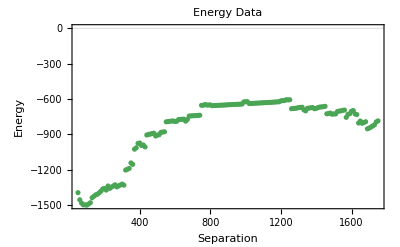

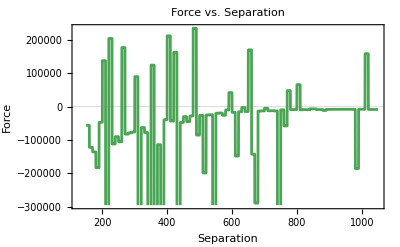

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

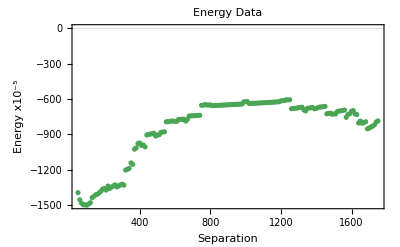

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
Close[stream];
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
|
```